# μLang — Computationally Generating a Morphologically Average Conlang using Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

We start with a simple word and and using translations provided by the Wolfram Language. In this case, I’m using “language.”

```mathematica
KEYWORD = "river";
```

Generate translations of KEYWORD into many languages

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
rawTranslations//Short
```

{Mandarin Chinese→河,Hindi→नदी,Spanish→río,Russian→река,Indonesian→sungai,Portuguese→rio,Bengali→নদী,Arabic→نَهر,Malay→sungai,Japanese→川,French→rivière,German→Fluss°,Urdu→دریا,Javanese→kali,Turkish→nehir,«151»,Chiripá→ry,Nanai→махгбо,Choctaw→hatcha,Mansi→ас,Koryak→в'эем,Ho-Chunk→ní xáte,Karaim→чырпыкъ,Karon Dori→эҥер,Bai→kare,Batak→sunge,Gilyak→эри,Alabama→pahnichoba,Judeo-Crimean Tatar→чай,Latin→flumen,Classical Quechua→mayu}

Standardize all translated words — Transliterate to the Roman alphabet and ensure all words are lowercase

```mathematica
translatedList=DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]]
```

{he,nadi,rio,reka,sungai,nahr,chuan,riviere,drya,kali,nehir,gang,aru,maena,fiume,mto,rzeka,rika,kogi,ho,walungan,cay,rau,ilog,rivier,suba,osimiri,nai,folyo,songay,maayo,webi,potami,rwizi,rwdkhanh,dah,umfula,mstinje,fium,raka,flod,karayan,umujezi,umlambo,ebale,get,riu,elga,jalan,derya,rijeka,gada,joki,nhr,rieka,umujyezi,elv,deriyava,noka,ibai,mdinare,dex,salog,salo,nambu,tyyk,darya,upe,krueng,aineet,isa,rivero,laga,jylga,syv,kaloro,oroche,vaitafe,mulonga,khusi,ster,jogi,abhainn,mulambo,hi,lebu,sere,lej,rivye,osuin,bale,inyan,kalog,xmara,ribiero,u,uciwai,a,laj,awa,dera,sug,usi,omugga,flum,bira,xukur,as,veem,ry,mahgbo,hatcha,kare,sunge,eri,pahnichoba,caj,flumen,mayu}

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{h,e},{n,a,d,i},{r,i,o},{r,e,k,a},{s,u,n,g,a,i},{n,a,h,r},«107»,{s,u,n,g,e},{e,r,i},{p,a,h,n,i,c,h,o,b,a},{c,a,j},{f,l,u,m,e,n},{m,a,y,u}}

Find the average length of all words

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

5

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly.

```mathematica
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
augmentedLists//Short
```

{{h,e,-,-,-},{n,a,d,i,-},{r,i,o,-,-},{r,e,k,a,-},{s,u,n,g,a},{n,a,h,r,-},«108»,{e,r,i,-,-},{p,a,h,n,i},{c,a,j,-,-},{f,l,u,m,e},{m,a,y,u,-}}

Transpose the charList for easier calculation of the most frequent character at every position

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word

```mathematica
mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

rauaa

While this method does “work,” it is rather boring. It always produces one very predictable word and isn’t very creative. To generate an exciting lexicon, we should explore some other methods.

## Most Common Digram

My first thought was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram.

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
positionedDigrams//Short
```

{{1,he},{1,na},{2,ad},{3,di},{1,ri},{2,io},{1,re},{2,ek},{3,ka},{1,su},{2,un},{3,ng},{4,ga},{5,ai},«405»,{6,ch},{7,ho},{8,ob},{9,ba},{1,ca},{2,aj},{1,fl},{2,lu},{3,um},{4,me},{5,en},{1,ma},{2,ay},{3,yu}}

Group digrams by their position

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|he→1,na→4,ri→10,re→1,su→4,ch→1,dr→1,ka→5,ne→1,ga→2,ar→1,ma→4,fi→2,mt→1,rz→1,ko→1,ho→1,wa→1,ca→2,ra→2,il→1,os→2,fo→1,so→1,we→1,po→1,rw→2,da→2,um→4,ms→1,fl→3,eb→1,ge→1,el→2,ja→1,de→4,jo→2,nh→1,no→1,ib→1,md→1,sa→2,ty→1,up→1,kr→1,ai→1,is→1,la→2,jy→1,sy→1,or→1,va→1,mu→2,kh→1,st→1,ab→1,hi→1,le→2,se→1,ba→1,in→1,xm→1,uc→1,aw→1,us→1,om→1,bi→1,xu→1,as→1,ve→1,ry→1,ha→1,er→1,pa→1|>

Get the most frequent digram in each position

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{ri},{al},{lo},{ga},{er},{re},{an},{ob},{ba}}

Generate new words by combining the most frequent digrams

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]

mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{ri,rial,riallo,rialloga}

This isn’t great either. While we get some pronounceable words, this method is very basic and relies on the most common digram. What if we want a little more variety in our words?

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique. A genetic algorithm has a few parts:

Population: This is a set of possible solutions. In this case, the population is a List of possible “average” words. We will generate the starting population by randomly combining digrams from the original word list. Then, we will evolve the population.

Fitness: This a function that evaluates how “good” any individual is. Our fitness metric will measure how similar an individual is to the starting word list.

Selection: We want to select the top n most fit individuals to continue into the next population

Recombination: We can combine two “parents”, or parts of two words from a generation to form a “child” for the succeeding generation

Mutation: Each generation, we randomly alter some words to simulate random genetic mutation. This introduces more variability in the population and allows the population to explore a greater breadth of possibilities. We will randomly replace a letter or digram in some  randomly chosen words.

Define important variables. populationSize is the size of the population each generation and mutationRate

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=500;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
```

{{ri,ka,na,su,ma},{al,ah,iv,er,iu},{lo,ka,ng,um,ra},{ga,an,ie,am,na},{er,ng,ai,ha,ya},{re,ga,an,bo,ri},{an,nh,zi,va,ho},{ob},{ba}}

```mathematica
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
```

5

Our fitness function will calculate the average Levenshtein distance between a candidate word and each word in the original word list

```mathematica
(*fitnessFunction[candidate_String]:=-N[Mean[EditDistance[candidate,#]&/@words]];*)
```

```mathematica
fitnessFunction[candidate_String]:=Module[{maxDistance},
  maxDistance=Max[EditDistance[candidate,#] & /@ words];
  1-N[Mean[EditDistance[candidate,#] & /@ words]/maxDistance]
]
```

The fitness of a word similar to possible KEYWORD translations is significantly greater than a completely unrelated fitness word

```mathematica
fitnessFunction[WordTranslation[KEYWORD, "Spanish"][[1]]]
```

0.515406

```mathematica
fitnessFunction["random word"]
```

0.102368

Here is our list of possible digrams

```mathematica
charSet
```

{ri,ka,na,su,ma,al,ah,iv,er,iu,lo,ka,ng,um,ra,ga,an,ie,am,na,er,ng,ai,ha,ya,re,ga,an,bo,ri,an,nh,zi,va,ho,ob,ba}

Create our original population by randomly combining digrams

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
Print["Initial population--"];
population=Table[randomString[],{populationSize}]
```

Initial population--

{kaivga,zibori,reivma,ahbanana,ngkavazi,umya,anka,raob,ivvabana,anga,ngra,hogaba,anrirean,ngnh,nangka,iesure,ngloboan,ansu,amzi,nayaraan,sungieer,analumiu,erribo,basu,umiv,aniuriya,ivalzina,erergaiu,ngie,nasuna,alsuga,amloan,renh,riivriai,angara,anannh,rier,anersuie,anzi,ivnaan,obnhre,haernhbo,ahhaer,ivivri,ivai,yazimaka,yari,sunhrari,alalng,obumerva,obzi,ersuamng,gakariiv,obnaiuer,ieam,erga,baya,hababo,rinaloya,riri,gaal,ahharasu,reannh,kaiekazi,anma,nhan,rizi,aiholo,bohoer,erka,ngiv,alobka,riai,umloer,haobai,rivaiena,ivbana,obbo,hari,naer,hariyari,amba,airiumma,long,revamasu,riri,hona,kaivgari,gavaal,ganh,bangob,raiu,anri,alganhra,rasuie,kangobna,rereumya,yaan,kaalngsu,riziho}

With everything set up, we can simulate several hundred generations of evolution. Starting from a population of randomly pieced together digrams, we

```mathematica
allBest={};

Do[fitnesses=fitnessFunction/@population;
bestFitness=Max[fitnesses];
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
AppendTo[allBest,bestCandidate];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
onePointCrossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
twoPointCrossover[p1_,p2_]:=Module[{len,pt1,pt2,c1,c2},len=Min[StringLength[p1],StringLength[p2]];
{pt1,pt2}=Sort@RandomSample[Range[len],2];
c1=Characters[p1];
c2=Characters[p2];
StringJoin@Join[Take[c1,pt1-2],Take[c2,{pt1,pt2}],Drop[c1,pt2]]];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
children=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
population=children;,{gen,1,generations}];

(*Get the best word across all generations*)
bestWord=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWord];
Print["Fitness: ",fitnessFunction[bestWord]];
```

Best word found: rvar

Fitness: 0.565546

```mathematica
allBest//Short
```

{riai,rvar,rmye,rmmr,rurr,surr,ueram,rerr,umaae,rmer,rmalr,rbalr,rmeam,eraak,rvaar,euaer,ruger,«467»,rlaae,rlaae,rraer,sulag,rulag,rgrae,rumal,rlaar,rlaar,rkuae,rkuae,ryaam,rlgay,ryaae,rygae,reuan}

```mathematica
fitnessFunction/@allBest//Short
```

{0.543417,0.565546,0.562185,0.544538,0.557143,0.552941,«488»,0.537815,0.52437,0.529412,0.535294,0.536134,0.543697}

## Generation with Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2000  rounds:500  time:45s  examples/s:1450
data | ,,  training examples:119  processed examples:64000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:9.22×10^-1  error:33.1%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{ah,deri,hia,kalo}

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords,bestWord, mostDigramGenerated, mostFreqCharWord}]]
```

{ah,deri,hia,kalo,rvar,ri,rial,riallo,rialloga,rauaa}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
testList = Transliterate[{WordTranslation[KEYWORD, "Spanish"][[1]],WordTranslation[KEYWORD, "French"][[1]],WordTranslation[KEYWORD, "English"][[1]],WordTranslation[KEYWORD, "Romanian"][[1]], WordTranslation[KEYWORD, "Portuguese"][[1]], StringDrop[WordTranslation[KEYWORD, "German"][[1]],-1]}]
```

{rio,riviere,river,rau,rio,Fluss}

```mathematica
FeatureSpacePlot[testList,FeatureExtractor->extractor,LabelingFunction->Callout]
```

-Graphics-

```mathematica
FeatureSpacePlot[
  {Style[allPossibleWords,Blue],Style[{"test"},Red]},
  FeatureExtractor->extractor,
  LabelingFunction->Callout
]
```

-Graphics-

```mathematica
extractor["riu"]
```

1.1302

```mathematica
extractor["rial"]
```

5.3504

```mathematica
extractor["wljrdwjf"]
```

8.93611

```mathematica
extractor /@ translatedList
```

{1.41667,0.976933,1.16245,0.926861,0.734428,0.959662,0.83136,0.657723,0.952818,0.846127,0.700929,0.976703,1.12195,0.825721,0.802843,1.17031,0.819348,0.814154,0.962552,1.41137,0.631993,1.15666,1.1329,0.94653,0.753461,0.948343,0.704344,1.15057,0.837125,0.751572,0.852258,0.939958,0.729121,0.708899,0.599523,1.20444,0.740776,0.689052,0.935603,0.96161,0.843329,0.665254,0.664158,0.710848,0.849357,0.864707,1.1302,0.969835,0.82284,0.828558,0.738657,0.979119,0.973086,1.13469,0.814378,0.629102,1.17595,0.606818,0.948546,0.9657,0.679146,1.19393,0.848845,0.987882,0.716218,0.961022,0.812575,1.1254,0.705456,0.766289,1.15779,0.72943,0.972614,0.845915,1.1995,0.784856,0.730816,0.658832,0.661288,0.820541,0.987277,0.952786,0.679318,0.674323,1.43647,0.965198,0.973452,1.13066,0.849985,0.852348,0.98964,0.820239,0.835194,0.790814,0.673183,2.01674,0.749045,1.98211,1.15577,1.13465,0.926396,1.14557,1.17116,0.726498,0.963786,0.810125,0.887122,1.48432,0.967348,1.46527,0.746889,0.754305,0.928847,0.851374,1.11435,0.528277,1.11887,0.774907,0.980238}

```mathematica
translatedList
```

{he,nadi,rio,reka,sungai,nahr,chuan,riviere,drya,kali,nehir,gang,aru,maena,fiume,mto,rzeka,rika,kogi,ho,walungan,cay,rau,ilog,rivier,suba,osimiri,nai,folyo,songay,maayo,webi,potami,rwizi,rwdkhanh,dah,umfula,mstinje,fium,raka,flod,karayan,umujezi,umlambo,ebale,get,riu,elga,jalan,derya,rijeka,gada,joki,nhr,rieka,umujyezi,elv,deriyava,noka,ibai,mdinare,dex,salog,salo,nambu,tyyk,darya,upe,krueng,aineet,isa,rivero,laga,jylga,syv,kaloro,oroche,vaitafe,mulonga,khusi,ster,jogi,abhainn,mulambo,hi,lebu,sere,lej,rivye,osuin,bale,inyan,kalog,xmara,ribiero,u,uciwai,a,laj,awa,dera,sug,usi,omugga,flum,bira,xukur,as,veem,ry,mahgbo,hatcha,kare,sunge,eri,pahnichoba,caj,flumen,mayu}

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=fitnessFunction /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Fitness Heatmap: Larger is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```

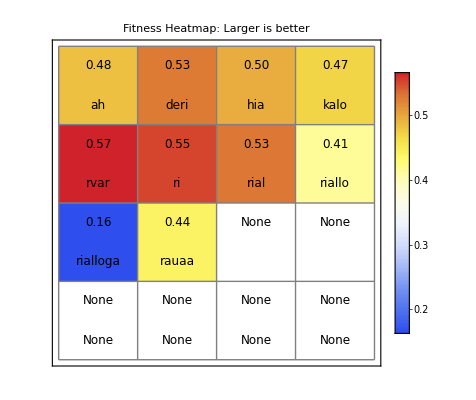

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Neural Net Feature Extractor Heatmap: Smaller is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```